```mathematica
rnorms1=RandomVariate[NormalDistribution[0,1],50]
```

{-0.337109,0.190578,-0.915637,0.683948,-1.62522,1.41678,-0.578764,0.77846,-0.204279,1.15687,0.2513,-0.466999,1.24878,0.967638,-0.738348,-0.842245,1.13056,-1.34594,-1.22627,-1.9256,0.255395,-0.00498991,1.10602,1.04161,-0.0244514,0.579781,0.225171,0.213229,-0.161628,0.111703,0.0669333,-0.834823,-1.25144,-0.949935,-0.767631,0.759459,0.360208,-0.202951,0.51818,1.68856,1.48063,-0.00489056,0.206369,0.624062,1.4627,-0.162746,0.0487944,-0.837791,0.861608,0.464795}

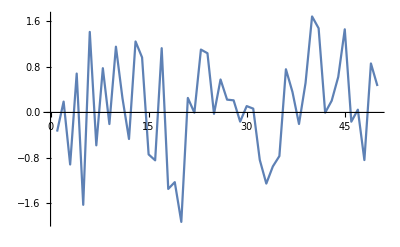

```mathematica
ListLinePlot[rnorms1]
```

```mathematica
rnorms2=Prepend[rnorms1,0]
```

{0,-0.337109,0.190578,-0.915637,0.683948,-1.62522,1.41678,-0.578764,0.77846,-0.204279,1.15687,0.2513,-0.466999,1.24878,0.967638,-0.738348,-0.842245,1.13056,-1.34594,-1.22627,-1.9256,0.255395,-0.00498991,1.10602,1.04161,-0.0244514,0.579781,0.225171,0.213229,-0.161628,0.111703,0.0669333,-0.834823,-1.25144,-0.949935,-0.767631,0.759459,0.360208,-0.202951,0.51818,1.68856,1.48063,-0.00489056,0.206369,0.624062,1.4627,-0.162746,0.0487944,-0.837791,0.861608,0.464795}

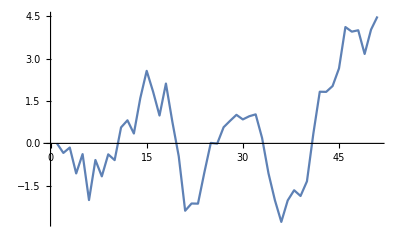

```mathematica
ListLinePlot[Accumulate[rnorms2]]
```

```mathematica
randomWalk[n_]:=Accumulate[Prepend[RandomVariate[NormalDistribution[0,1],n],0]]
```

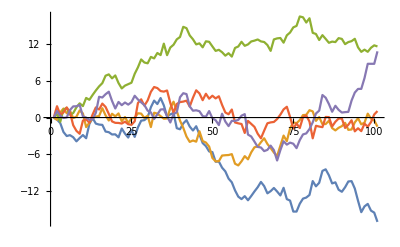

```mathematica
ListLinePlot[Table[randomWalk[100],{5}]]
```

```mathematica
rwalks=Table[randomWalk[100],{1000}];
```

```mathematica
final=rwalks[[All,-1]];
```

```mathematica
{Mean[final],StandardDeviation[final],Max[final],Min[final]}
```

{-0.308115,9.99489,40.414,-31.5513}